## Луд А. С.

## Лабораторная работа №5 : Численные расчёты в системе Mathematica

## 5.1

#### 5.1.а | Пробел выполняет роль знака умножения

```mathematica
3 5
```

15

#### 5.1.б | Введение дополнительных пробелом не изменяют результата вычислений

```mathematica
3   5
```

15

```mathematica
2+         7
```

9

#### 5.1.в | Целые, рациональные и иррациональные числа считаются заданными точно. Поэтому в выражениях, содержащих только такие числа, при обработке производятся лишь возможные упрощения, но сами они остаются точными и преобразуются в числа, заданные приближенно, только по команде пользователя

```mathematica
2/3
```

2/3

```mathematica
17^(1/2)
```

√17

#### 5.1.г | Действительные числа, содержащие десятичную точку, считаются заданными приближенно. Поэтому выражения, в которые входят действительные числа, вычисляются при обработке секции без специальной команды

```mathematica
3 /7.
```

0.428571

```mathematica
17.^(1/2)
```

4.12311

#### 5.1.д | Для изменения стандартного порядка выполнения операций используются скобки

```mathematica
5     (4-1)
```

15

## 5.2

#### 5.2.а | С помощью функции N вычислить 17^(1/2) с точностью до 200 значащих цифр. Провериться потом с помощью Precision

```mathematica
N[Sqrt[17],200]
```

4.1231056256176605498214098559740770251471992253736204343986335730949543463376215935878636508106842966845440409392141416153014208404158683630795481457469069776770232664362408630877905675723857082255214

```mathematica
Precision[%]
```

200.

#### 5.2.б | Найти приближенное значение числа с точностью до 40 значащих цифр. Вычислить насколько полученный результат отличается от ближайшего к нему целого числа

```mathematica
N[E^(Pi*Sqrt[163]),40]
```

2.625374126407687439999999999992500725972×10^17

```mathematica
Round[N[E^(Pi*Sqrt[163]),40]] - N[E^(Pi*Sqrt[163]),40]
```

7.499274028×10^-13

#### 5.2.в | Вычислить

```mathematica
(10*((10.8*10^3)/300)^(1/2) + 4)^(1/3)
```

4.

```mathematica
(10^-24 10^12)/10^-14 √(32768/2^9)
```

800

#### 5.2.г | Последовательно введите выражения | Справедливо ли неравенство

```mathematica
5>3
```

True

```mathematica
5<2
```

False

```mathematica
Pi^E>E^Pi
```

False

```mathematica
N[Pi^E]
```

22.4592

```mathematica
N[E^Pi]
```

23.1407

## 5.3

#### 5.3.а | Решить уравнения

```mathematica
NSolve[Sqrt[x+2]+4*x==4,x]
```

{{x→0.597111}}

```mathematica
NSolve[x^3-3  x^2+5 == 0, x]
```

{{x→-1.1038},{x→2.0519-0.565236 ⅈ},{x→2.0519+0.565236 ⅈ}}

#### 5.3.б | Решить системы уравнений

```mathematica
NSolve[{x^2+x*y+y^2==1,x^3+x^2*y+x*y^2+y^3==4},{x,y}]
```

{{x→-1.-1.41421 ⅈ,y→-1.+1.41421 ⅈ},{x→-1.+1.41421 ⅈ,y→-1.-1.41421 ⅈ},{x→1.6838+0.133552 ⅈ,y→-0.683802-1.13355 ⅈ},{x→1.6838-0.133552 ⅈ,y→-0.683802+1.13355 ⅈ},{x→-0.683802-1.13355 ⅈ,y→1.6838+0.133552 ⅈ},{x→-0.683802+1.13355 ⅈ,y→1.6838-0.133552 ⅈ}}

```mathematica
NSolve[{x-y^2+3*z==34,x+y-z==-1,-x+2*y+3*z==4},{x,y,z}]
```

{{x→9.25-10.2317 ⅈ,y→-3.5+4.09268 ⅈ,z→6.75-6.13901 ⅈ},{x→9.25+10.2317 ⅈ,y→-3.5-4.09268 ⅈ,z→6.75+6.13901 ⅈ}}

#### 5.3.в | Придумать уравнение или систему уравнений и найдите её численное решение

```mathematica
NSolve[{x^3+y^3+3*x^2*y+3*y^2*x==64,x+3*y==8}, {x,y},Reals]
```

{{x→2.,y→2.}}

## 5.4

#### Вариант 16 | 2cox(x)=exp(-2x) на отрезке x=>{-1,2}

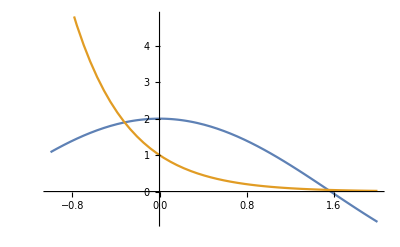

```mathematica
Plot[{2*Cos[x], Exp[-2*x]}, {x, -1,2}]
```

```mathematica
FindRoot[2*Cos[x]==Exp[-2*x],{x,-1,2}]
```

{x→1.54819}

## 5.5

#### Вариант 16 | y’’+2y’th(x)+3y=0, y(0)=-1, y’(0)=2 на отрезке x=>{-3,2}

```mathematica
funcy=NDSolve[{y''[x]+2*y'[x]*Tanh[x]+3*y[x]==0,y[0]==-1,y'[0]==2},y,{x,-3,2}]
```

{{y→InterpolatingFunction[…]}}

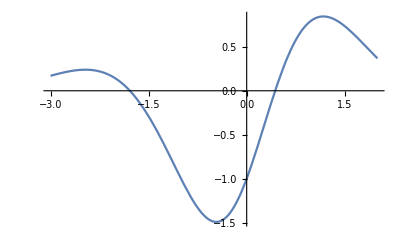

```mathematica
Plot[y[x]/.funcy,{x,-3,2}]
```

#### 5.5.a | Найдите на заданном отрезке корни уравнения y(x)=0

```mathematica
r1=FindRoot[y[x]/.funcy,{x,-1.8}]
```

{x→-1.78623}

```mathematica
r2=FindRoot[y[x]/.funcy,{x,0.4}]
```

{x→0.43521}

#### 5.5.б | Найдите значения производной y’(x) в точках, где y(x)=0

```mathematica
D[y[x]/.funcy,x]/.r1
```

{-0.798593}

```mathematica
D[y[x]/.funcy,x]/.r2
```

{2.23451}

#### 5.5.в | Выберите одну из точек, в которых производная функции y(x)=0, и вычислите значение функции в этой точке

```mathematica
LocalMaxim=FindRoot[D[y[x]/.funcy,x]==0,{x,1.2}](*Производная равна 0 в точках, где касательная к графику функции паралельна оси абсцисс(точки экстремума)*)
```

{x→1.17248}

```mathematica
y[x]/.funcy/.LocalMaxim
```

{0.845325}

#### 5.5.г | С помощью функции FindMinimum найдите точки, в которых функция y(x) имеет локальный минимум или максимум, и сравните полученные результаты со значениями, найденными в пункте ‘в’

```mathematica
FindMaximum[y[x]/.funcy,{x,1.2}]
```

{0.845325,{x→1.17248}}

## 5.6

#### 5.6.а | Задайте произвольные численные значения параметров a,b,c,d,e в следующих зависимостях: y(x)=a+b*x+c*x^2+d*x^3+e*x^4 и y(x)=a+b*x+c*sin(x)+d*cos(x). Используя функцию Table, определите список численных данных, каждый элемент которого содержит два элемента (x,y). Область изменения х и шаг выберите самостоятельно. С помощью функции Random внесите в каждой точке х случайное возмущение Дy

#### 1)

```mathematica
dat1=Table[{x,(10+8*x+6*x^2+4*x^3+2*x^4)(1+Random[Real,{-0.1,0.1}])},{x,0,4,0.2}]
```

{{0.,10.5187},{0.2,11.42},{0.4,13.6789},{0.6,16.6699},{0.8,23.6269},{1.,31.3871},{1.2,38.4652},{1.4,50.0734},{1.6,67.1007},{1.8,90.893},{2.,109.154},{2.2,138.092},{2.4,176.8},{2.6,219.488},{2.8,292.556},{3.,373.338},{3.2,422.861},{3.4,579.051},{3.6,655.773},{3.8,704.222},{4.,863.034}}

#### 2)

```mathematica
dat2=Table[{x,(20+38*x+62*Sin[x]+25*Cos[x])(1+Random[Real,{-0.1,0.1}])},{x,0,5,0.2}]
```

{{0.,43.8998},{0.2,68.4703},{0.4,88.4279},{0.6,98.5111},{0.8,102.623},{1.,125.827},{1.2,139.292},{1.4,149.384},{1.6,137.448},{1.8,134.311},{2.,139.366},{2.2,137.118},{2.4,139.583},{2.6,139.829},{2.8,115.745},{3.,110.07},{3.2,112.448},{3.4,106.229},{3.6,106.249},{3.8,113.837},{4.,109.227},{4.2,118.613},{4.4,117.047},{4.6,132.266},{4.8,132.679},{5.,170.872}}

#### 5.6.б | Изобразите полученные точки на координатной плоскости

```mathematica
1)
```

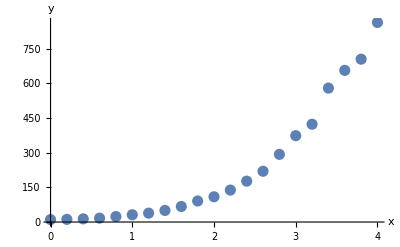

```mathematica
y1=ListPlot[dat1,PlotStyle->PointSize[0.02],AxesLabel->{"x","y"}]
```

```mathematica
2)
```

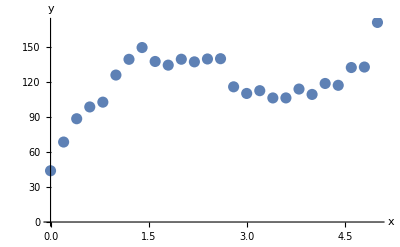

```mathematica
p1=ListPlot[dat2,PlotStyle->PointSize[0.02],AxesLabel->{"x","y"}]
```

#### 5.6.в | С помощью функции Fit найдите наилучшую кривую, аппроксимирующую численные данные

```mathematica
1)
```

```mathematica
apr1=Fit[dat1,{1,x,x^2,x^3,x^4},x]
```

2.96152+69.3083 x-83.4879 x^2+44.9511 x^3-3.77015 x^4

```mathematica
apr2=Fit[dat1,{1,x,Sin[x]},x](*экспериментальные точки*)
```

53.7897+132.85 x-231.623 Sin[x]

```mathematica
2)
```

```mathematica
aproc1=Fit[dat2,{1,x,Sin[x],Cos[x]},x]
```

18.82+38.7809 x+27.3373 Cos[x]+62.254 Sin[x]

```mathematica
aproc2=Fit[dat2,{1,x,x^2,x^3},x](*экспериментальные точки*)
```

39.615+141.529 x-61.1291 x^2+7.53786 x^3

#### 5.6.г | На одной координатной плоскости изобразите найденную кривую вместе с экспериментальными точками

```mathematica
1)
```

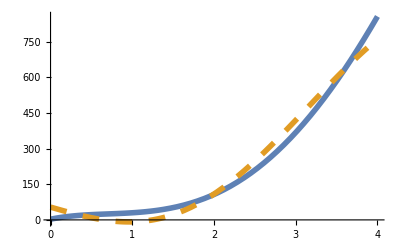

```mathematica
y2=Plot[{apr1,apr2},{x,0,4},
PlotStyle->{{Thickness[0.01]},{Thickness[0.01],Dashing[{0.03}]}}]
```

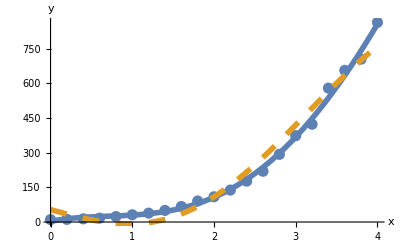

```mathematica
Show[y1,y2]
```

```mathematica
2)
```

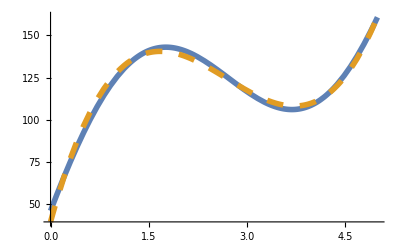

```mathematica
p2=Plot[{aproc1,aproc2},{x,0,5},
PlotStyle->{{Thickness[0.01]},{Thickness[0.01],Dashing[{0.03}]}}]
```

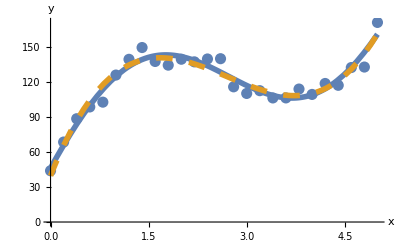

```mathematica
Show[p1,p2]
```